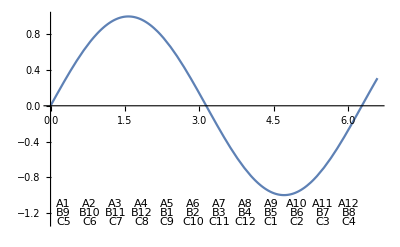

(π/6 | 1-(√3)/2 | 0.134 | 0.134 | 34 | 137 | 549 | 8780 | 8780
π/3 | 1/2 | 0.5 | 0.366 | 128 | 512 | 2048 | 32768 | 23988
π/2 | 1 | 1. | 0.5 | 256 | 1024 | 4096 | 65536 | 32768
(2 π)/3 | 3/2 | 1.5 | 0.5 | 384 | 1536 | 6144 | 98304 | 32768
(5 π)/6 | 1/2 (2+√3) | 1.866 | 0.366 | 478 | 1911 | 7643 | 122292 | 23988
π | 2 | 2. | 0.134 | 512 | 2048 | 8192 | 131072 | 8780
(7 π)/6 | 1/2 (2+√3) | 1.866 | -0.134 | 478 | 1911 | 7643 | 122292 | -8780
(4 π)/3 | 3/2 | 1.5 | -0.366 | 384 | 1536 | 6144 | 98304 | -23988
(3 π)/2 | 1 | 1. | -0.5 | 256 | 1024 | 4096 | 65536 | -32768
(5 π)/3 | 1/2 | 0.5 | -0.5 | 128 | 512 | 2048 | 32768 | -32768
(11 π)/6 | 1-(√3)/2 | 0.134 | -0.366 | 34 | 137 | 549 | 8780 | -23988
2 π | 0 | 0. | -0.134 | 0 | 0 | 0 | 0 | -8780)

```mathematica
SS[offset_,length_,high_]:=Table[
{x,high*Sin[x*π+offset*π]},
{x,0,length,0.03}];
A1=SS[0,3,1];
AAA=Plot[Sin[x],{x,0,2.1π},
GridLines->{{
{1/6 π,Green},
{2/6 π,Green},
{3/6 π,Green},
{4/6 π,Green},
{5/6 π,Green},
{7/6 π,Green},
{8/6 π,Green},
{9/6 π,Green},
{10/6 π,Green},
{11/6 π,Green},
{1π,Red},
{2π,Red},
{3π,Red}
},None}

];
TC[x_,offset_]:=If[(x+offset)>24,
(x+offset)-24,
If[(x+offset)>12,
(x+offset)-12,(x+offset)]];
TS[abc_,x_,offset_]:=abc<>ToString[TC[x,offset]];
TT[abc_,offs_,high_]:=Table[Graphics[Text[TS[abc,x,offs],{(x-0.5)/6*π,high}]],{x,1,12}];
CCa=TT["A",0,-1.1];
CCb=TT["B",8,-1.2];
CCc=TT["C",16,-1.3];
Show[AAA,CCa,CCb,CCc
,PlotRange->All
]
ClearAll;
II3[yy2_]:=Integrate[Sin[x],{x,0,yy2}];
II4[yy2_]:=Integrate[Sin[x],{x,yy2-π/6,yy2}];
II9=Table[{
yy,
II3[yy],
Round[1000*II3[yy]]/1000.0,
Round[1000*II4[yy]]/1000.0,
Round[II3[yy]*(2^8)],
Round[II3[yy]*(2^10)],
Round[II3[yy]*(2^12)],
Round[II3[yy]*(2^16)],
Round[II4[yy]*(2^16)]

},{yy,1/6 π,2π,1/6 π}];
II9//MatrixForm
```